```mathematica
data1=Import["/Users/yakimkina/_workspace/_mgtu/cpp/methods_for_solving_nonlinear_equations/cmake-build-debug/output/test4_diagram.csv", {"CSV", "Data"},"Numeric"->True];
data2=Import["/Users/yakimkina/_workspace/_mgtu/cpp/methods_for_solving_nonlinear_equations/cmake-build-debug/output/test5_diagram.csv", {"CSV", "Data"},"Numeric"->True];
```

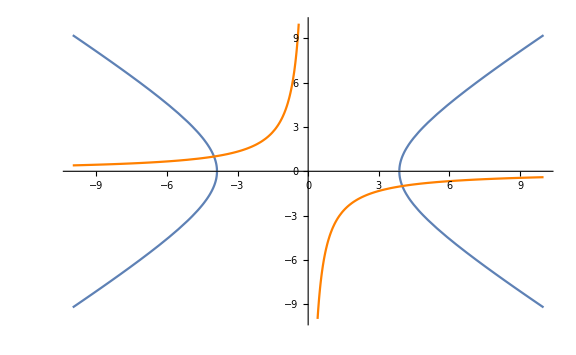

```mathematica
p4 = Plot[Sqrt[x1^2- 15],{x1, -10, 10}, PlotRange -> {-10, 10}];
p5 = Plot[-Sqrt[x1^2- 15],{x1, -10, 10}, PlotRange -> {-10, 10}];
p6 = Plot[-4/x1,{x1, -10, 10}, PlotStyle->  Orange, PlotRange -> {-10, 10}];
Show[p4, p5, p6, ImageSize->Large]
```

```mathematica
p1 = ArrayPlot[data1, ColorFunction-> GrayLevel,(*ColorRules->{30->Red},*)PlotLegends->Range[30], PlotRange->{0, 30}, ImageSize->500];
p2 = ArrayPlot[data2, ColorFunction->GrayLevel, (*ColorRules->{30->Red},*)PlotLegends->Range[30], PlotRange->{0, 30}, ImageSize->500];
(*Export["/Users/yakimkina/_workspace/_mgtu/cpp/methods_for_solving_nonlinear_equations/test4_chisl[0.8].pdf", p1]*)
(*Export["/Users/yakimkina/_workspace/_mgtu/cpp/methods_for_solving_nonlinear_equations/test5_chisl[0.8].pdf", p2]*)
```

```mathematica
s1 = ContourPlot[x1^2- x2^2 - 15 == 0, {x1, -10, 10}, {x2, -10,10}];
s2 = ContourPlot[x1 x2 + 4== 0, {x1, -10, 10}, {x2, -10, 10}, ContourStyle-> Orange];
g1 = ListDensityPlot[data1,ColorFunction->GrayLevel, (*ColorRules->{30->Red},*)PlotLegends->Range[30], PlotRange->{0, 30}, ImageSize->500, InterpolationOrder-> 0];

s3 = ContourPlot[x1^2+ x2^2 +x1 + x2 - 8 == 0, {x1, -10, 10}, {x2, -10, 10}];
s4 = ContourPlot[x1^2+ x2^2 +x1 x2 - 7 == 0, {x1, -10, 10}, {x2, -10, 10}, ContourStyle-> Orange];
g2 = ListDensityPlot[data2,ColorFunction-> GrayLevel, (*ColorRules->{30->Red},*)PlotLegends->Range[30], PlotRange->{0, 30}, ImageSize->500, InterpolationOrder-> 0];
p3 = Show[g1, s1, s2, ImageSize -> 500]
p8 = Show[g2, s3, s4, ImageSize -> 500]
(*Export["/Users/yakimkina/_workspace/_mgtu/cpp/methods_for_solving_nonlinear_equations/test4_anal.pdf", p3]
Export["/Users/yakimkina/_workspace/_mgtu/cpp/methods_for_solving_nonlinear_equations/test5_anal.pdf", p8]*)
```

-Graphics-

-Graphics-

```mathematica
(*ParamericPlot3D[x1^2 - x2^2 -15 = 0, {x1, -10, 10}, {x2, -10, 10}]*)
```

Set::write: Tag Plus in -15+x1^2-x2^2 is Protected.

ParamericPlot3D[0,{x1,-10,10},{x2,-10,10}]